# Homework 4

Name: Muhammad Salah Shatla

ID: 201500059

## Problem 1

100 ⅇ^(-t/τa)

(5 (ⅇ^(-t/τb) (τa-21 τb)+20 ⅇ^(-t/τa) τb))/(τa-τb)

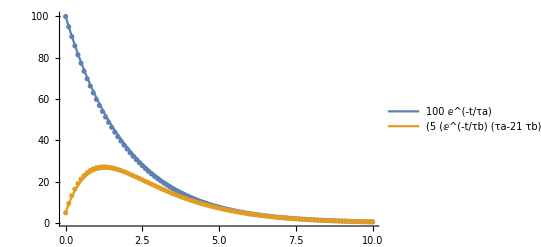

```mathematica
ClearAll["Global`*"];
τlistA={2,1,1,1}; τlistB={1,1,10,0.1}; τAl=Length[τlistA]; τBl=Length[τlistB];
tstart=0; tend=10; dt=0.1; NAinitial=100; NBinitial=5; 
tlist=Range[tstart,tend,dt]; tl=Length[tlist];
NAlist=0 tlist; NBlist=0 tlist;
NAlist[[1]]=NAinitial; NBlist[[1]]=NBinitial;
listfigAnum=0 τlistA;

(*Analytic Solution*)
sol=Flatten[FullSimplify[{Subscript[N, A][t],Subscript[N, B][t]}/.DSolve[{Subscript[N, A]'[t]==(-Subscript[N, A][t])/τa,Subscript[N, B]'[t]==(Subscript[N, A][t])/τa-(Subscript[N, B][t])/τb,Subscript[N, A][0]==NAinitial,Subscript[N, B][0]==NBinitial},{Subscript[N, A][t],Subscript[N, B][t]},t]]];
Subscript[p, A]=sol[[1]]
Subscript[p, B]=sol[[2]] 

analyticfig=Plot[{Subscript[p, A]/.τa->τlistA[[1]],Subscript[p, B]/.{τa->τlistA[[1]],τb->τlistB[[1]]}},{t,tstart,tend},PlotRange->All,PlotLegends->{Subscript[p, A],Subscript[p, B]}];

(*Numerical Solution*)
Do[NAlist[[i]]=NAlist[[i-1]]-NAlist[[i-1]]/τlistA[[1]] dt;NBlist[[i]]=NBlist[[i-1]]+(NAlist[[i-1]]/τlistA[[1]]-NBlist[[i-1]]/τlistB[[1]]) dt,{i,2,tl}];

numericfig=ListPlot[{Table[{tlist[[i]],NAlist[[i]]},{i,tl}],Table[{tlist[[i]],NBlist[[i]]},{i,tl}]},PlotRange->All];


Show[analyticfig,numericfig,PlotRange->All]
```

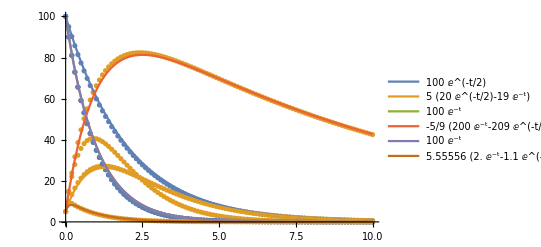

The Analytical Solution for τ_A=2,τ_B=1 & τ_A=τ_B=1 & 10τ_A=τ_B=10 & 0.1τ_A=τ_B=0.1:

The solution for the case: τ_A=2 , τ_B=1

N_A(t)= 100 ⅇ^(-t/2) and N_B(t)= 5 (-19 ⅇ^-t+20 ⅇ^(-t/2))

The solution for the case: τ_A=1 , τ_B=1

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

N_A(t)= 100 ⅇ^-t and N_B(t)= Indeterminate

The solution for the case: 10τ_A=τ_B=10

N_A(t)= 100 ⅇ^-t And, N_B(t)= -5/9 (200 ⅇ^-t-209 ⅇ^(-t/10))

The solution for the case: 0.1τ_A=τ_B=0.1

N_A(t)= 100 ⅇ^-t And, N_B(t)= 5.55556 (-1.1 ⅇ^(-10. t)+2. ⅇ^-t)

```mathematica
(*For Subscript[τ, A]=Subscript[τ, B]=1 & 10 Subscript[τ, A]=Subscript[τ, B]=10 & 0.1 Subscript[τ, A]=Subscript[τ, B]=0.1*)
(*The Numerical Solution*)
Do[
Do[NAlist[[i]]=NAlist[[i-1]]-NAlist[[i-1]]/τlistA[[j]] dt;NBlist[[i]]=NBlist[[i-1]]+(NAlist[[i-1]]/τlistA[[j]]-NBlist[[i-1]]/τlistB[[j]]) dt,{i,2,tl}];listfigAnum[[j]]=ListPlot[{Table[{tlist[[k]],NAlist[[k]]},{k,tl}],Table[{tlist[[k]],NBlist[[k]]},{k,tl}]},PlotRange->All],{j,τAl}];


(*The Analytical Solution*)
figanalytic=Plot[{Subscript[p, A]/.τa->τlistA[[1]],Subscript[p, B]/.{τa->τlistA[[1]],τb->τlistB[[1]]},Subscript[p, A]/.τa->τlistA[[3]],Subscript[p, B]/.{τa->τlistA[[3]],τb->τlistB[[3]]},Subscript[p, A]/.τa->τlistA[[4]],Subscript[p, B]/.{τa->τlistA[[4]],τb->τlistB[[4]]}},{t,tstart,tend},PlotRange->All,PlotLegends->{Subscript[p, A]/.τa->τlistA[[1]],Subscript[p, B]/.{τa->τlistA[[1]],τb->τlistB[[1]]},Subscript[p, A]/.τa->τlistA[[3]],Subscript[p, B]/.{τa->τlistA[[3]],τb->τlistB[[3]]},Subscript[p, A]/.τa->τlistA[[4]],Subscript[p, B]/.{τa->τlistA[[4]],τb->τlistB[[4]]}}];

Show[listfigAnum,figanalytic,PlotRange->All]

Print["The Analytical Solution for τ_A=2,τ_B=1 & τ_A=τ_B=1 & 10τ_A=τ_B=10 & 0.1τ_A=τ_B=0.1: "]
Print["\nThe solution for the case: τ_A=2 , τ_B=1"]
Print["N_A(t)= ",Subscript[p, A,Subscript[τ, A]=1]=sol[[1]]/.τa->τlistA[[1]]," and N_B(t)= ", Subscript[p, B,Subscript[τ, B]=1]=sol[[2]] /.{τa->τlistA[[1]],τb->τlistB[[1]]}]

Print["\nThe solution for the case: τ_A=1 , τ_B=1"]
Print["N_A(t)= ",Subscript[p, A,Subscript[τ, A]=1]=sol[[1]]/.τa->τlistA[[2]]," and N_B(t)= ", Subscript[p, B,Subscript[τ, B]=1]=sol[[2]] /.{τa->τlistA[[2]],τb->τlistB[[2]]}]

Print["\nThe solution for the case: 10τ_A=τ_B=10"]
Print["N_A(t)= ",Subscript[p, A,Subscript[τ, A]=1]=sol[[1]]/.τa->τlistA[[3]]," And, N_B(t)= ",Subscript[p, B,Subscript[τ, B]=1]=sol[[2]] /.{τa->τlistA[[3]],τb->τlistB[[3]]}]

Print["\nThe solution for the case: 0.1τ_A=τ_B=0.1"]
Print["N_A(t)= ",Subscript[p, A,Subscript[τ, A]=1]=sol[[1]]/.τa->τlistA[[4]]," And, N_B(t)= ",Subscript[p, B,Subscript[τ, B]=1]=sol[[2]] /.{τa->τlistA[[4]],τb->τlistB[[4]]}]
```

## Problem 2

The General Solution is:

N_A(t)= 1/2 (C[1]+ⅇ^(-(2 t)/τ) (C[1]-C[2])+C[2])

N_B(t)= 1/2 (C[1]+C[2]+ⅇ^(-(2 t)/τ) (-C[1]+C[2]))

For N_A(t=0)=100 and N_B(t=0)=200,

N_A(t)= 1/2 (300-100 ⅇ^(-(2 t)/τ)) and, N_B(t)=1/2 (300+100 ⅇ^(-(2 t)/τ))

For N_A(t=0)=50 and N_B(t=0)=30,

N_A(t)= 1/2 (80+20 ⅇ^(-(2 t)/τ)) and, N_B(t)=1/2 (80-20 ⅇ^(-(2 t)/τ))

For N_A(t=0)=10 and N_B(t=0)=50,

N_A(t)= 1/2 (60-40 ⅇ^(-(2 t)/τ)) and, N_B(t)=1/2 (60+40 ⅇ^(-(2 t)/τ))

Using Mathematica NDSolve function

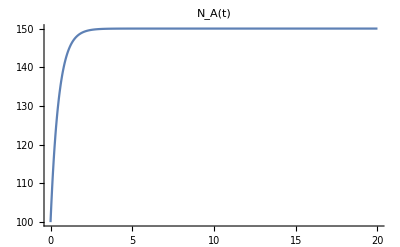

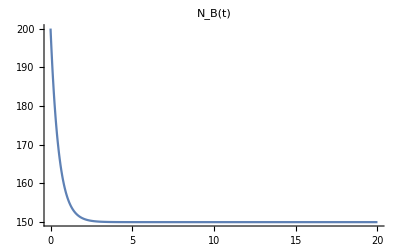

The numeric Solution for three different pairs of initial conditions:

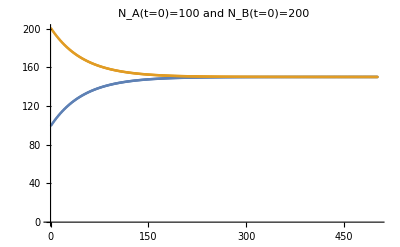

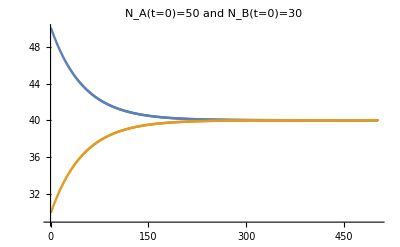

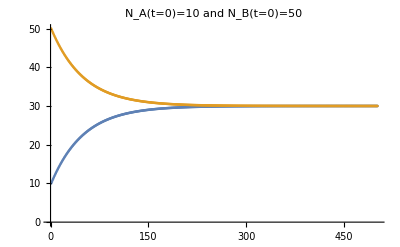

from the graphs above, it is obvious that both N_A(t) and N_B(t)approach a comman value which is the steady state value that differs according to the initial conditions of both functions as illustrated above by three examples with three different conditions.

```mathematica
(*(Subscript[dN, A][t])/dt=Subscript[N, B]/τ-Subscript[N, A]/τ, (Subscript[dN, B][t])/dt=Subscript[N, A]/τ-Subscript[N, B]/τ*)
(*Solving This system Exactly*)
ClearAll["Global`*"];
initialA={100, 50, 10}; initialB={200,30,50};
Print["\nThe General Solution is: "]
Sol2=Flatten[FullSimplify[{Subscript[N, A][t],Subscript[N, B][t]}/.DSolve[{Subscript[N, A]'[t]==(Subscript[N, B][t])/τ-(Subscript[N, A][t])/τ,Subscript[N, B]'[t]==(Subscript[N, A][t])/τ-(Subscript[N, B][t])/τ},{Subscript[N, A][t],Subscript[N, B][t]},t]]];
Print["N_A(t)= ",Sol2[[1]]]
Print["N_B(t)= ",Sol2[[2]]]

Print["\nFor N_A(t=0)=100 and N_B(t=0)=200,  "]
Print["N_A(t)= ",Sol2[[1]]/.{C[1]->initialA[[1]],C[2]->initialB[[1]]}," and, N_B(t)=",Sol2[[2]]/.{C[1]->initialA[[1]],C[2]->initialB[[1]]}]
(*Plot[Sol2[[1]]/.{C[1]->initialA[[1]],C[2]->initialB[[1]],τ->1},{t,0,20}]*)

Print["\nFor N_A(t=0)=50 and N_B(t=0)=30,  "]
Print["N_A(t)= ",Sol2[[1]]/.{C[1]->initialA[[2]],C[2]->initialB[[2]]}," and, N_B(t)=",Sol2[[2]]/.{C[1]->initialA[[2]],C[2]->initialB[[2]]}]

Print["\nFor N_A(t=0)=10 and N_B(t=0)=50,  "]
Print["N_A(t)= ",Sol2[[1]]/.{C[1]->initialA[[3]],C[2]->initialB[[3]]}," and, N_B(t)=",Sol2[[2]]/.{C[1]->initialA[[3]],C[2]->initialB[[3]]}]

(*Using NDSolve :*)
Print["\nUsing Mathematica NDSolve function"]
s=Flatten[NDSolve[{Subscript[N, A]'[t]==(Subscript[N, B][t])/τ-(Subscript[N, A][t])/τ,Subscript[N, B]'[t]==(Subscript[N, A][t])/τ-(Subscript[N, B][t])/τ,Subscript[N, A][0]==initialA[[1]],Subscript[N, B][0]==initialB[[1]],τ==1},{Subscript[N, A][t],Subscript[N, B][t]},{t,20}]];
Plot[Evaluate[Subscript[N, A][t]/.s[[1]]],{t,0,20},PlotLabel->"N_A(t)",PlotRange->All]
Plot[Evaluate[Subscript[N, B][t]/.s[[2]]],{t,0,20},PlotLabel->"N_B(t)",PlotRange->All]

(*My Code using Euler's Method*)
tstart2=0;tend2=5;dt2=0.01;
τ2={1}; τ2l=Length[τ2];
tlist2=Range[tstart2,tend2,dt2]; tlist2l=Length[tlist2];
NAlist2=0 tlist2; NBlist2=0 tlist2;
listfigA2=Array[0,Length[initialA]];
listfigB2=Array[0,Length[initialB]];

Do[NAlist2[[1]]=initialA[[j]]; NBlist2[[1]]=initialB[[j]];Do[NAlist2[[i]]=NAlist2[[i-1]]+((NBlist2[[i-1]]-NAlist2[[i-1]])/τ2[[1]]) dt2;NBlist2[[i]]=NBlist2[[i-1]]+((NAlist2[[i-1]]-NBlist2[[i-1]])/τ2[[1]]) dt2,{i,2,tlist2l}];listfigA2[[j]]=NAlist2;listfigB2[[j]]=NBlist2,{j,Length[initialA]}];


Print["The numeric Solution for three different pairs of initial conditions: "] 

ListPlot[{listfigA2[[1]],listfigB2[[1]]},PlotRange->Full,PlotLabel->"N_A(t=0)=100 and N_B(t=0)=200"]

ListPlot[{listfigA2[[2]],listfigB2[[2]]},PlotRange->Full,PlotLabel->"N_A(t=0)=50 and N_B(t=0)=30"]

ListPlot[{listfigA2[[3]],listfigB2[[3]]},PlotRange->Full,PlotLabel->"N_A(t=0)=10 and N_B(t=0)=50"]

(*Check for the behaviour of Subscript[N, A](t) and Subscript[N, B](t) as t -> ∞*)

Print["from the graphs above, it is obvious that both N_A(t) and N_B(t)approach a comman value which is the steady state value that differs according to the initial conditions of both functions as illustrated above by three examples with three different conditions."]
```